## Poisson-equation approach, Series treatment -- (0, 2Pi) integration, all periodic BC

### set up from origin

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0-bmu(Cos[theta1]+Cos[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qx1-bmu^2(Cos[theta1]+Cos[theta2])^2+Qx0 bmu(Cos[theta1]+Cos[theta2]))
```

```mathematica
(*Clear[H0,H0c,H0s,I0cch,I0csh,I0sch,I0ssh,A0c,dA0c]*)
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
pv10[bJx_,bmux_,theta1_,theta2_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,theta1_,theta2_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]

H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
A1[0,j_,theta1_]:=Integrate[h1[0,j](theta1-t1),{t1,0,theta1}]
A1[n_,j_,theta1_]:=2/n Integrate[h1[n,j]Sinh[n/2(theta1-t1)],{t1,0,theta1}]-2Cosh[n/2 theta1]/(n Sinh[n Pi])Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
dA1[0,j_,theta1_]:=Integrate[h1[0,j],{t1,0,theta1}]
dA1[n_,j_,theta1_]:=Integrate[h1[n,j]Cosh[n/2(theta1-t1)],{t1,0,theta1}]-2Sinh[n/2 theta1]/Sinh[n Pi]Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
```

```mathematica
Flatten[Table[{n,j,H0[0,j,t1_]:=Release[H0[0,j,t1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0c[n,j,t1_]:=Release[H0c[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0s[n,j,t1_]:=Release[H0s[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0cch[n,j,t1_]:=Release[I0cch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0sch[n,j,t1_]:=Release[I0sch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0csh[n,j,t1_]:=Release[I0csh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0ssh[n,j,t1_]:=Release[I0ssh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,A0c[n,j,theta1_]:=Release[A0c[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,dA0c[0,j,theta1_]:=Release[dA0c[0,j,theta1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,h1[n,j]=H1[n,j,t1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm;
```

```mathematica
Flatten[Table[{n,j,da0[n,j]=dA0[n,j,theta1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm;
```

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

```mathematica
Qx0=0;
```

### set up from analytica sum

```mathematica
(*Ax0[theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) (-1+Cos[theta1])
dAx0[theta1_]:=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1]*)
```

```mathematica
Axc0[n_,theta1_]:=1/(bJ+4 bJ n^4)2 bmu (((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])
Axc0[0,theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) (-1+Cos[theta1]);
```

```mathematica
dAxc0[n_,theta1_]:=1/(1+4 n^4)bmu (2 BesselI[n,bJ] (-Cos[n theta1] Sin[theta1]+n (1-2 n^2) Cos[theta1] Sin[n theta1])+BesselI[-1+n,bJ] ((1+n) Sin[(-1+n) theta1]+2 n^3 Sin[theta1-n theta1])+(-1+n-2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
dAxc0[0,theta1_]:=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1]
```

```mathematica
Axs0[n_,theta1_]:=1/(1+4 n^4)bmu ((1+2 n (1+n)) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (-2 n Cos[n theta1] Sin[theta1]+(1+2 n^2) Cos[theta1] Sin[n theta1])+(1+2 (-1+n) n) BesselI[1+n,bJ] Sin[theta1+n theta1])
Axs0[0,theta1_]:=0
```

```mathematica
dAxs0[n_,theta1_]:=1/(bJ+4 bJ n^4)(-2 bmu n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Cos[theta1] Cos[n theta1]-2 bmu (bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])
dAxs0[0,theta1_]:=0
```

Axs0 is tested

```mathematica
pvx10[theta1_,theta2_,nmax_]:=Sum[dAxs0[n,theta1]Sin[n theta2]+dAxc0[n,theta1]Cos[n theta2],{n,0,nmax}]
pvx20[theta1_,theta2_,nmax_]:=Sum[n Axs0[n,theta1]Cos[n theta2]-n Axc0[n,theta1]Sin[n theta2],{n,1,nmax}]
pvx10n[theta1_,theta2_,n_]:=dAxs0[n,theta1]Sin[n theta2]+dAxc0[n,theta1]Cos[n theta2]
pvx20n[theta1_,theta2_,n_]:=n Axs0[n,theta1]Cos[n theta2]-n Axc0[n,theta1]Sin[n theta2]
```

### Comparisn by plot

```mathematica
nmax=1;
bJ=bmu=1;
jmax=2;
myt2=Pi/3;
```

```mathematica
pvx10[ t2,myt2,nmax]//N
```

-1.71774

```mathematica
t2=2;
{t2,pvx10[ t2,myt2,nmax]Exp[Cos[t2-myt2]],pvx20[ myt2,t2,nmax]Exp[Cos[t2-myt2]],pv10[1,1,t2,myt2]Exp[Cos[t2-myt2]],pv20[1,1,myt2,t2]Exp[Cos[t2-myt2]]}//N
```

{2.,-3.06612,-2.94862,-2.92412,-2.81934}

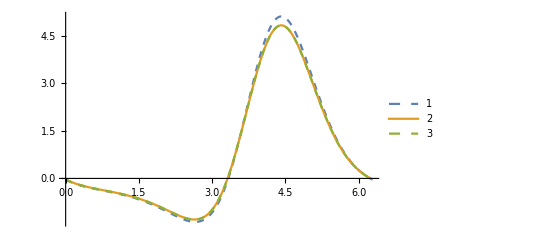

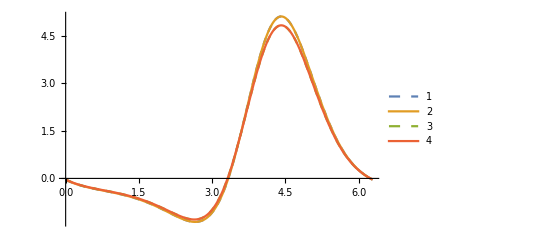

```mathematica
nmax=5;
bJ=bmu=1;
jmax=2;
myt2=1.3*Pi;
Plot[{pvx10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic]
Plot[{pvx10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvx20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]],pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic]
```

```mathematica
nmax
```

5

```mathematica
Plot[{pvx10[ theta2,myt2,nmax],pv10[1,1,theta2,myt2]},{theta2,0,2Pi}]
```

```mathematica
myt2=myt1=Pi/2.5;
Table[{pvx10[myt1,myt2,n],pvx20[myt2,myt1,n]},{n,0,5}]
```

{{-1.7416,0},{-2.00824,-1.60828},{-1.90958,-1.85181},{-1.89026,-1.88363},{-1.88777,-1.88714},{-1.88752,-1.88747}}

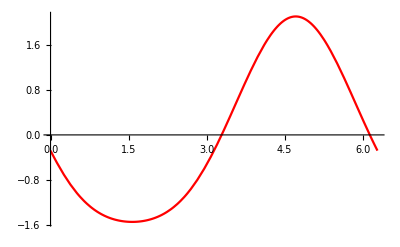

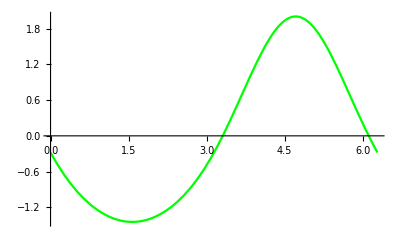

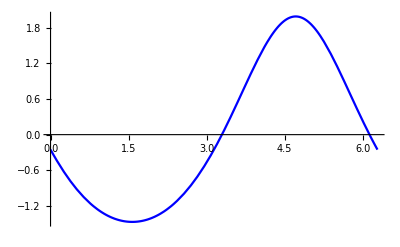

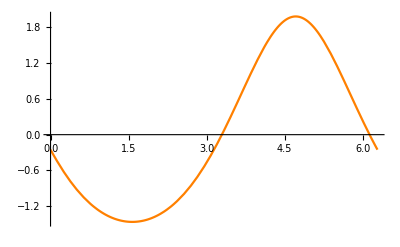

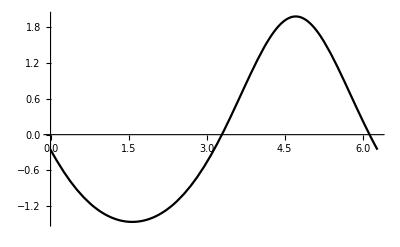

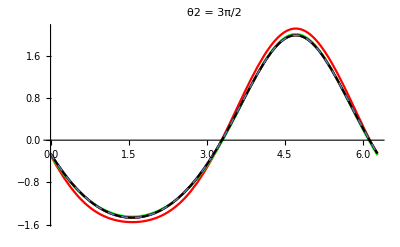

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pvx10[theta1,myt2,nmax],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=2;plot[nmax]=Plot[pvx10[theta1,myt2,nmax],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=3;plot[nmax]=Plot[pvx10[theta1,myt2,nmax],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=4;plot[nmax]=Plot[pvx10[theta1,myt2,nmax],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=5;plot[nmax]=Plot[pvx10[theta1,myt2,nmax],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
plot[nmax+1]=Plot[pvx20[myt2,theta2,nmax],{theta2,0,2Pi},PlotStyle->{Dashed,Thick}];
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```